Abstract-algebra lattices
They have two operations, meet (mt) and join (jn). They are both semilattices on the lattice elements; they are commutative, associative, and idempotent (a*a = a for all elements a).
They are interrelated with absorption:
a mt (a jn b) = a
a jn (a mt b) = a
This property is equivalent to a mt b = a <-> a jn b = b

They satisfy partial ordering:
a <= b from a = a mt b and equivalently b = a jn b

Lowest element: zero of mt, identity of jn
Highest element: zero of jn, identity of mt

Dual of lattice: interchange mt and jn.
Self-dual: same lattice results.

Semimodular lattices
a mt b <: a implies b <: a jn b

where a <: b means a < b with no c such that a < c < b. Thus, a and b are neighbors with none in between.

This is “upper semimodular”; its dual condition is “lower semimodular”:
b <: a jn b implies a mt b <: a

Both together are equivalent to modularity for finite lattices.

Modular lattices
a <= b implies that for all x, a jn (x mt b) = (a jn x) mt b

Examples:
* Submodules of a module over a ring
* Subgroups of an abelian group
* Normal subgroups of a group
* (Not in general: subgroups of a group)
* Subspaces of vector spaces
* Ideals of a ring

Distributive lattices
meet and join are distributive over each other
Examples:
* Numbers, min, max
* Positive integers: gcd, lcm
* Sets: intersection, union (every distributive lattice ~ some lattice of sets)

(plain) > semimodular > modular > distributive

Smallest non-modular lattice: pentagon lattice N5 -- no modular lattice contains it
Smallest non-distributive modular lattice: diamond lattice M3 -- no distributive lattice contains it

Lattices can be assembled from sequences of other lattices with end nodes being merged. If that is possible for some lattice, then it is vertically decomposable. Otherwise, it is vertically indecomposable.

Graded: all paths from one end to each element have the same length.
Geometric: semimodular and “atomistic” / “atomic”

For vertical decomposition, uses algorithm inspired by
PartitionTransform.nb
PartCompArray[], PartIrredArray[]
but with ordered partitions
OrdPartCompArray[]

Number of vertically indecomposable distributive lattices on n nodes.  - had to be recalculated
Series base: 1

Counts
The counts of them are in variable numdata, with the arg a string that contains at least one of these substrings:
lat - lattice
vid - vertically indecomposable - cannot be split into a sequence of sublattices
smd - semimodular
mod - modular
dst - distributive
pln - planar
grd - graded
geom - geometric
lbl - labeled nodes

### Theorems and Proofs

Every finite semilattice has a zero.
Construct z = a * b * c * ... over all the elements. That is possible for every finite semilattice, though only for some infinite ones.

Find a*z for any element a. a*z = a*a*b*c*... = a*b*c*... = z. Thus, if it z is the sero of the semilattice.

If a semilattice has an identity, then removing it will leave a semilattice.
Let us say that it is not possible. Then there is at least one pair of elements where a*b = e where neither a nor b is e.
Multiply by a:
a*a*b = a*b = e
a*e = a
Contradiction. The identity-less algebra will be closed, thus being a semilattice.

A consequence is that one can adjoin an identity element to any finite semilattice, thus giving a lattice.

The zero of meet is the identity of join, and vice versa.
The zero of meet: z mt a = z, By meet-join flipping, z jn a = a
Thus z is the identity of join.
Interchanging meet and join shows that the zero of join is the identity of meet.

### Sources

Online Encyclopedia of Integer Sequences
https://oeis.org/A006966 - Number of lattices on n unlabeled nodes.
https://oeis.org/A229202 - Number of semimodular lattices on n nodes
https://oeis.org/A058800 - Vertically indecomposable lattices on n unlabeled nodes. 
https://oeis.org/A006981 - a(n) is the number of unlabeled modular lattices on n nodes.
https://oeis.org/A342132 - Number of unlabeled vertically indecomposable modular lattices on n nodes.
https://oeis.org/A006982 - Number of unlabeled distributive lattices on n nodes.
https://oeis.org/A072361 - Number of vertically indecomposable distributive lattices on n nodes. 
https://oeis.org/A343161 - Number of planar distributive lattices with n nodes.
https://oeis.org/A345734 - Number of planar vertically indecomposable distributive lattices with n nodes.
https://oeis.org/A278691 - Number of graded lattices on n nodes.
https://oeis.org/A281574 - Number of geometric lattices on n nodes. 
https://oeis.org/A055512 - Lattices with n labeled elements.
https://oeis.org/A058803 - Vertically indecomposable lattices on n labeled nodes.

Counting Finite Lattices | SpringerLink
https://link.springer.com/article/10.1007/PL00013837
Counting_Finite_Lattices.pdf
https://www.researchgate.net/profile/Jobst-Heitzig/publication/225384356_Counting_Finite_Lattices/links/0912f505788c49a251000000/Counting-Finite-Lattices.pdf?origin=publication_detail

## Functions

```mathematica
OrdPartCompArrayOrig[narr_] := Module[{nlen,n,ptrws,pt,pti},
nlen = Length[narr];
Table[ptrws = IntegerPartitions[n];
Expand[Sum[pt = Tally[ptrw]; Length[ptrw]!*Product[Power[narr[[pti[[1]]]],pti[[2]]]/pti[[2]]!,
{pti,pt}],
{ptrw,ptrws}]],
{n,nlen}]
]
```

```mathematica
OrdPartIrredArrayOrig[narr_] := Module[{irrval,nlen,n,ptrws,pt,pti},
nlen = Length[narr];
Do[ptrws = IntegerPartitions[n,{2,n}];
irrval[n] = Expand[narr[[n]] - Sum[pt = Tally[ptrw]; Length[ptrw]!*Product[Power[irrval[pti[[1]]],pti[[2]]]/pti[[2]]!,
{pti,pt}],
{ptrw,ptrws}]],
{n,nlen}];
Array[irrval,nlen]
]
```

```mathematica
OrdPartCompArray[narr_] := Module[{nmax,rsarf},
nmax = Length[narr];
Do[rsarf[n] = Expand[narr[[n]] + Sum[narr[[k]]*rsarf[n-k],{k,n-1}]],
{n,nmax}];
Array[rsarf,nmax]
]
```

```mathematica
OrdPartIrredArray[narr_] := Module[{nmax,rsarf},
nmax = Length[narr];
Do[rsarf[n] = Expand[narr[[n]] - Sum[narr[[k]]*rsarf[n-k],{k,n-1}]],
{n,nmax}];
Array[rsarf,nmax]
]
```

### Tests

```mathematica
(* Arg is some array to do tests on *)
```

```mathematica
OrdPartCompIrredTest[narr_] := OrdPartCompArray[OrdPartIrredArray[narr]] - narr
```

```mathematica
OrdPartIrredCompTest[narr_] := OrdPartIrredArray[OrdPartCompArray[narr]] - narr
```

```mathematica
OrdPartCompArrayTest[narr_] := OrdPartCompArrayOrig[narr] - OrdPartCompArray[narr]
```

```mathematica
OrdPartIrredArrayTest[narr_] := OrdPartIrredArrayOrig[narr] - OrdPartIrredArray[narr]
```

## Data

```mathematica
numdata["lat"] = {1,1,1,2,5,15,53,222,1078,5994,37622,262776,2018305,16873364,152233518,1471613387,15150569446,165269824761,1901910625578,23003059864006};
```

```mathematica
numdata["lat vid"] = {1,1,0,1,2,7,27,126,664,3954,26190,190754,1514332,12998035,119803771,1178740932,12316480222,136060611189,1582930919092,19328253734491};
```

```mathematica
numdata["lat smd"] = {1,1,1,2,4,8,17,38,88,212,530,1376,3693,10232,29231,85906,259291,802308,2540635,8220218,27134483,91258141,312324027,1086545705,3838581926};
```

```mathematica
numdata["lat smd vid"] = {1,1,0,1,1,2,4,9,21,53,139,384,1088,3186,9596,29601,93462,301265,990083,3312563,11270507,38955164,136660780,486223384,1753185150}; (* from Jipsen-Lawless with the last three values calculated here *)
```

```mathematica
numdata["lat mod"] = {1,1,1,2,4,8,16,34,72,157,343,766,1718,3899,8898,20475,47321,110024,256791,601991,1415768,3340847,7904700,18752943,44588803,106247120,253644319,606603025,1453029516,3485707007,8373273835,20139498217,48496079939,116905715114,282098869730};
```

```mathematica
numdata["lat mod vid"] = {1,1,0,1,1,2,3,7,12,28,54,127,266,614,1356,3134,7091,16482,37929,88622,206295,484445,1136897,2682451,6333249,15005945,35595805,84649515,201560350,480845007,1148537092,2747477575,6579923491,15777658535,37871501929};
```

```mathematica
numdata["lat dst"] = {1,1,1,2,3,5,8,15,26,47,82,151,269,494,891,1639,2978,5483,10006,18428,33749,62162,114083,210189,386292,711811,1309475,2413144,4442221,8186962,15077454,27789108,51193086,94357143,173859936,320462062,590555664,1088548290,2006193418,3697997558,6815841849,12563729268,23157428823,42686759863,78682454720,145038561665,267348052028,492815778109,908414736485};
```

```mathematica
numdata["lat dst vid"] = {1,1,0,1,0,1,0,3,1,6,2,16,8,42,28,112,93,311,295,869,939,2454,2931,7032,9036,20301,27701,58929,84413,172104,255919,504637,773511,1484392,2331180,4378773,7009288,12944347,21039961,38328890,63067623,113651785,188831922,337361112,564890985,1002268019,1688673026,2979703035,5045200597};
```

```mathematica
numdata["lat pln"]= {1,1,1,2,3,5,8,14,24,42,72,127,221,390,684,1207,2125,3753,6620,11698,20659,36518};
```

```mathematica
numdata["lat pln vid"] = {1,1,0,1,0,1,0,2,1,4,2,9,6,21,18,48,50,114,135,277,358,681};
```

```mathematica
numdata["lat grd"] = {1,1,1,2,4,9,22,60,176,565,1980,7528,30843,135248,630004,3097780,15991395,86267557,484446620,2822677523,17017165987};
```

```mathematica
numdata["lat geom"] = {1,1,0,1,1,1,1,2,1,2,1,3,2,2,3,5,3,4,5,6,6,8,9,16,16,21,29,45,50,95,136,220,392,680,1270,2530,4991};
```

```mathematica
numdata["lat lbl"] = {1,2,6,36,380,6390,157962,5396888,243179064,13938711210,987858368750,84613071940452,8597251494954564,1020353444641839854,139627532137612581090,21788453795572514675760,3840596246648027262079472,758435490711709577216754642};
```

```mathematica
numdata["lat lbl vid"] = {1,2,0,12,140,2910,83202,3170216,154933704,9441522810,701275774430,62304994315212,6517432341289740,791949368757587222,110496962589020946330,17525486812000086847440};
```

### Tests

```mathematica
vidtest[lbl_] := OrdPartCompArray[Rest[numdata[lbl <> " vid"]]] - Rest[numdata[lbl]]
```

```mathematica
vidtest["lat"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vidtest["lat smd"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vidtest["lat mod"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vidtest["lat dst"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vidtest["lat pln"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Analysis

```mathematica
lblplot[lblfunc_,lbls_] := ListLogPlot[lblfunc /@ lbls,Joined->True,PlotLegends->lbls]
```

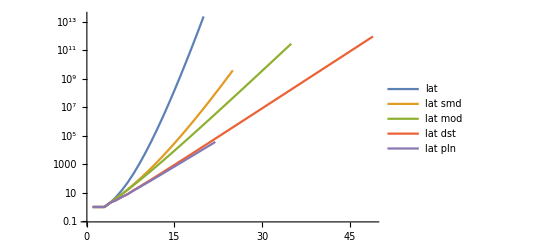

```mathematica
lblplot[numdata,{"lat","lat smd","lat mod","lat dst","lat pln"}]
```

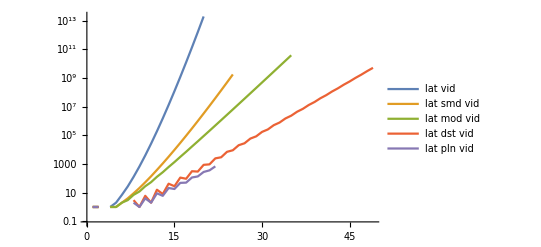

```mathematica
lblplot[numdata,{"lat vid","lat smd vid","lat mod vid","lat dst vid","lat pln vid"}]
```

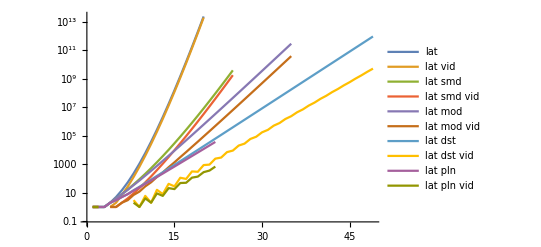

```mathematica
lblplot[numdata,{"lat","lat vid","lat smd","lat smd vid","lat mod","lat mod vid","lat dst","lat dst vid","lat pln","lat pln vid"}]
```

```mathematica
ndtbl[lbls_,maxnum_] := TableForm[Table[Take[numdata[lbl],maxnum],{lbl,lbls}],TableHeadings->{lbls,Range[maxnum]}]
```

```mathematica
ndtbl[{"lat","lat smd","lat mod","lat dst","lat pln"},12]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
lat | 1 | 1 | 1 | 2 | 5 | 15 | 53 | 222 | 1078 | 5994 | 37622 | 262776
lat smd | 1 | 1 | 1 | 2 | 4 | 8 | 17 | 38 | 88 | 212 | 530 | 1376
lat mod | 1 | 1 | 1 | 2 | 4 | 8 | 16 | 34 | 72 | 157 | 343 | 766
lat dst | 1 | 1 | 1 | 2 | 3 | 5 | 8 | 15 | 26 | 47 | 82 | 151
lat pln | 1 | 1 | 1 | 2 | 3 | 5 | 8 | 14 | 24 | 42 | 72 | 127

```mathematica
ndtbl[{"lat vid","lat smd vid","lat mod vid","lat dst vid","lat pln vid"},12]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
lat vid | 1 | 1 | 0 | 1 | 2 | 7 | 27 | 126 | 664 | 3954 | 26190 | 190754
lat smd vid | 1 | 1 | 0 | 1 | 1 | 2 | 4 | 9 | 21 | 53 | 139 | 384
lat mod vid | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 7 | 12 | 28 | 54 | 127
lat dst vid | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 3 | 1 | 6 | 2 | 16
lat pln vid | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 2 | 1 | 4 | 2 | 9

```mathematica
ndtbl[{"lat","lat vid","lat smd","lat smd vid","lat mod","lat mod vid","lat dst","lat dst vid","lat pln","lat pln vid"},12]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
lat | 1 | 1 | 1 | 2 | 5 | 15 | 53 | 222 | 1078 | 5994 | 37622 | 262776
lat vid | 1 | 1 | 0 | 1 | 2 | 7 | 27 | 126 | 664 | 3954 | 26190 | 190754
lat smd | 1 | 1 | 1 | 2 | 4 | 8 | 17 | 38 | 88 | 212 | 530 | 1376
lat smd vid | 1 | 1 | 0 | 1 | 1 | 2 | 4 | 9 | 21 | 53 | 139 | 384
lat mod | 1 | 1 | 1 | 2 | 4 | 8 | 16 | 34 | 72 | 157 | 343 | 766
lat mod vid | 1 | 1 | 0 | 1 | 1 | 2 | 3 | 7 | 12 | 28 | 54 | 127
lat dst | 1 | 1 | 1 | 2 | 3 | 5 | 8 | 15 | 26 | 47 | 82 | 151
lat dst vid | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 3 | 1 | 6 | 2 | 16
lat pln | 1 | 1 | 1 | 2 | 3 | 5 | 8 | 14 | 24 | 42 | 72 | 127
lat pln vid | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 2 | 1 | 4 | 2 | 9

```mathematica
drat[x_] := Rest[x]/Most[x]
```

```mathematica
drnd[x_] := drat[numdata[x]]
```

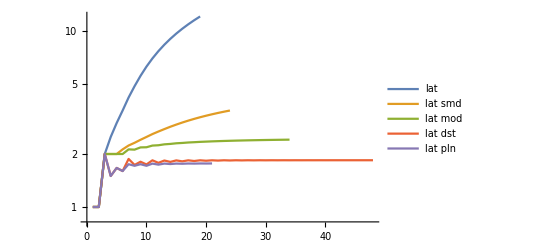

```mathematica
lblplot[drnd,{"lat","lat smd","lat mod","lat dst","lat pln"}]
```

```mathematica
addvid[x_] := x <> " vid"
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

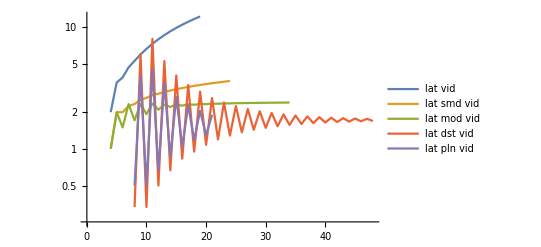

```mathematica
lblplot[drnd,addvid /@ {"lat","lat smd","lat mod","lat dst","lat pln"}]
```

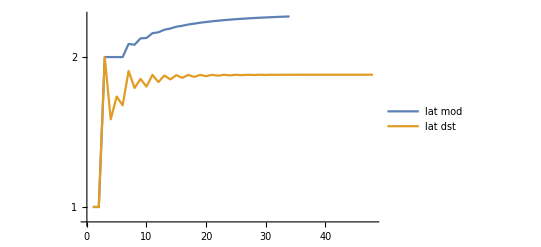

```mathematica
lblplot[drnd,{"lat mod","lat dst"}]
```

```mathematica
vidrat[lbl_] := N[numdata[addvid[lbl]]]/N[numdata[lbl]]
```

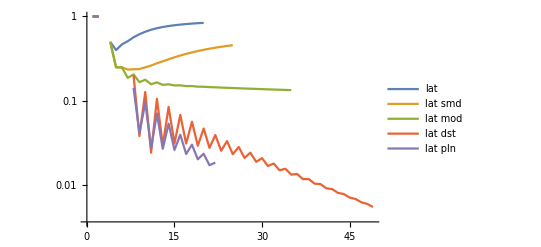

```mathematica
lblplot[vidrat,{"lat","lat smd","lat mod","lat dst","lat pln"}]
```

```mathematica
lbllinplot[lblfunc_,lbls_] := ListPlot[lblfunc /@ lbls,Joined->True,PlotLegends->lbls]
```

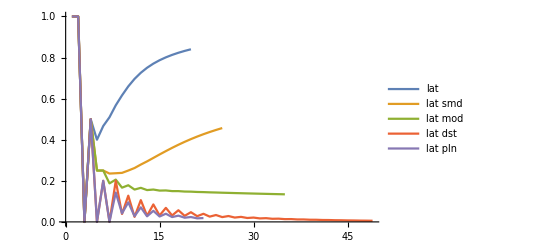

```mathematica
lbllinplot[vidrat,{"lat","lat smd","lat mod","lat dst","lat pln"}]
```

```mathematica
(* Comparison to estimated asymptotic forms *)
```

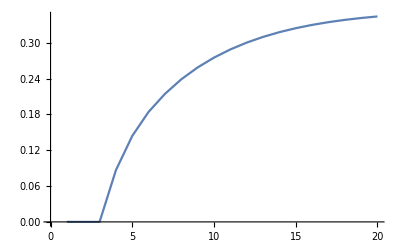

```mathematica
ListPlot[Log[N[numdata["lat"]]]/Range[Length[numdata["lat"]]]^1.5,Joined->True]
```

```mathematica
ndrtfc[nd1_,nd2_] := N[Take[nd1,#]/Take[nd2,#]/Range[#]!]& @ Min[Length[nd1],Length[nd2]]
```

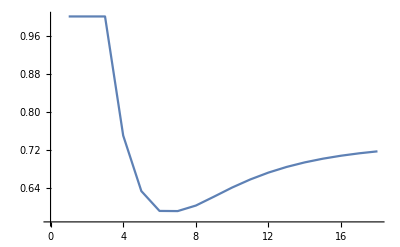

```mathematica
ListPlot[ndrtfc[numdata["lat lbl"],numdata["lat"]],Joined->True]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

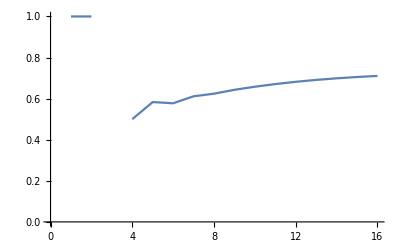

```mathematica
ListPlot[ndrtfc[numdata["lat lbl vid"],numdata["lat vid"]],Joined->True]
```

## Generation

### Brute Force

```mathematica
isassoc[mtab_] := Module[{n,i,j,k},
n = Length[mtab];
And @@ Flatten[Table[mtab[[i,mtab[[j,k]]]] == mtab[[mtab[[i,j]],k]],{i,n},{j,n},{k,n}]]
]
```

```mathematica
isassoc[{{1,1},{2,1}}]
```

False

```mathematica
(* Make table template: ident on one end, zero on the other end, diagonal is idempotent *)
```

```mathematica
mttmpl["meet",n_] := Table[Which[i==1,1,i==n,j,True,Which[j==1,1,j==n,i,j==i,i,True,0]],{i,n},{j,n}]
```

```mathematica
mttmpl["join",n_] := Table[Which[i==1,j,i==n,n,True,Which[j==1,i,j==n,n,j==i,i,True,0]],{i,n},{j,n}]
```

```mathematica
(* Table fill *)
```

```mathematica
mtfill[n_,vals_] := If[n>3,Join[ConstantArray[0,{2,n}],Table[Join[{0},PadRight[vals[[k(k-1)/2+1;;k(k+1)/2]],n-1,0]],{k,n-3}],ConstantArray[0,{1,n}]],ConstantArray[0,n*{1,1}]]
```

```mathematica
mtflsym[n_,vals_] := (# + Transpose[#])& @ mtfill[n,vals]
```

```mathematica
mtasm[type_,n_,vals_] := mttmpl[type,n] + mtflsym[n,vals]
```

```mathematica
mtasmtest[type_,n_,vals_] := If[isassoc[#],#,Nothing]& @ mtasm[type,n,vals]
```

```mathematica
mtxtvals["meet",n_] := Range[1,n-1]
```

```mathematica
mtxtvals["join",n_] := Range[2,n]
```

```mathematica
slat[type_,n_] := mtasmtest[type,n,#]& /@ If[n>3,Tuples[mtxtvals[type,n],(n-2)(n-3)/2],{{}}]
```

```mathematica
isabs[n_,m1_,m2_] := And @@ Flatten[Table[{m1[[i,m2[[i,j]]]]==i,m2[[i,m1[[i,j]]]]==i},{i,n},{j,n}]]
```

```mathematica
rawlattices[n_] := Module[{slmt,sljn},
slmt = slat["meet",n]; sljn = slat["join",n];
Flatten[Table[If[isabs[n,t1,t2],{t1,t2},Nothing],{t1,slmt},{t2,sljn}],1]
]
```

```mathematica
latperm[lat_,perm_] := Module[{n,invperm},
n = Length[perm];
invperm = ConstantArray[0,n];
Do[invperm[[perm[[i]]]] = i,{i,n}];
Map[#[[perm]]&,Map[#[[perm]]&,Map[invperm[[#]]&,lat,{3}],{2}],{1}]
]
```

```mathematica
rawlatperms[lat_] := Module[{n,perms},
n = Length[First[lat]];
perms = If[n≥3,Join[{1},#,{n}]& /@ Permutations[Range[2,n-1]],{Range[n]}];
latperm[lat,#]& /@ perms
]
```

```mathematica
latperms[lat_] := Union[rawlatperms[lat]]
```

```mathematica
canonlatperm[lat_] := First[latperms[lat]]
```

```mathematica
lattices[n_] := Union[canonlatperm /@ rawlattices[n]]
```

```mathematica
Map[MatrixForm,lattices[1],{2}]
```

{{(1),(1)}}

```mathematica
Map[MatrixForm,lattices[2],{2}]
```

{{(1 | 1
1 | 2),(1 | 2
2 | 2)}}

```mathematica
Map[MatrixForm,lattices[3],{2}]
```

{{(1 | 1 | 1
1 | 2 | 2
1 | 2 | 3),(1 | 2 | 3
2 | 2 | 3
3 | 3 | 3)}}

```mathematica
Map[MatrixForm,lattices[4],{2}]
```

{{(1 | 1 | 1 | 1
1 | 2 | 1 | 2
1 | 1 | 3 | 3
1 | 2 | 3 | 4),(1 | 2 | 3 | 4
2 | 2 | 4 | 4
3 | 4 | 3 | 4
4 | 4 | 4 | 4)},{(1 | 1 | 1 | 1
1 | 2 | 2 | 2
1 | 2 | 3 | 3
1 | 2 | 3 | 4),(1 | 2 | 3 | 4
2 | 2 | 3 | 4
3 | 3 | 3 | 4
4 | 4 | 4 | 4)}}

```mathematica
Map[MatrixForm,lattices[5],{2}]
```

{{(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 2
1 | 1 | 3 | 1 | 3
1 | 1 | 1 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 5 | 5 | 5
3 | 5 | 3 | 5 | 5
4 | 5 | 5 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 2
1 | 1 | 3 | 3 | 3
1 | 1 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 5 | 5 | 5
3 | 5 | 3 | 4 | 5
4 | 5 | 4 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 2
1 | 1 | 3 | 3 | 3
1 | 2 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 4 | 4 | 5
3 | 4 | 3 | 4 | 5
4 | 4 | 4 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 2 | 3
1 | 2 | 2 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 3 | 4 | 5
3 | 3 | 3 | 5 | 5
4 | 4 | 5 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 3 | 3
1 | 2 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 3 | 4 | 5
3 | 3 | 3 | 4 | 5
4 | 4 | 4 | 4 | 5
5 | 5 | 5 | 5 | 5)}}

```mathematica
isdistrib[lat_] := Module[{n,m1,m2},
n = Length[First[lat]];
{m1,m2} = lat;
And @@ Flatten[Table[{m1[[i,m2[[j,k]]]]==m2[[m1[[i,j]],m1[[i,k]]]],m2[[i,m1[[j,k]]]]==m1[[m2[[i,j]],m2[[i,k]]]]},{i,n},{j,n},{k,n}]]
]
```

```mathematica
dstrlats[n_] := Select[lattices[n],isdistrib]
```

```mathematica
isdistrib /@ lattices[5]
```

{False,False,True,True,True}

```mathematica
Map[Union,dstrlats[1],{3}]
```

{{{{1}},{{1}}}}

```mathematica
Map[Union,dstrlats[2],{3}]
```

{{{{1},{1,2}},{{1,2},{2}}}}

```mathematica
Map[Union,dstrlats[3],{3}]
```

{{{{1},{1,2},{1,2,3}},{{1,2,3},{2,3},{3}}}}

```mathematica
Map[Union,dstrlats[4],{3}]
```

{{{{1},{1,2},{1,3},{1,2,3,4}},{{1,2,3,4},{2,4},{3,4},{4}}},{{{1},{1,2},{1,2,3},{1,2,3,4}},{{1,2,3,4},{2,3,4},{3,4},{4}}}}

```mathematica
Map[Union,dstrlats[5],{3}]
```

{{{{1},{1,2},{1,3},{1,2,3,4},{1,2,3,4,5}},{{1,2,3,4,5},{2,4,5},{3,4,5},{4,5},{5}}},{{{1},{1,2},{1,2,3},{1,2,4},{1,2,3,4,5}},{{1,2,3,4,5},{2,3,4,5},{3,5},{4,5},{5}}},{{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}},{{1,2,3,4,5},{2,3,4,5},{3,4,5},{4,5},{5}}}}

```mathematica
latlks[lmat_,lk_] := Module[{n},
n = Length[lmat];
Flatten[Table[If[j≠i,If[lmat[[i,j]] == Switch[lk,1,i,2,j],{i,j},Nothing],Nothing],{i,n},{j,n}],1]
]
```

```mathematica
latlks[lat_] :=Table[latlks[lat[[lk]],lk],{lk,{1,2}}]
```

```mathematica
(* Tests the lattice linking *)
```

```mathematica
latlktest[llks_] := And @@ Flatten[{Table[lk[[1]]<lk[[2]],{lk,llks[[1]]}],llks[[2]]==llks[[1]]}]
```

```mathematica
Table[latlktest /@ (latlks /@ lattices[k]),{k,5}]
```

{{True},{True},{True},{True,True},{True,True,True,True,True}}

```mathematica
(* Try to remove every link that's composed of more than one link *)
```

```mathematica
lkssimp[lks_] := Module[{n,present},
If[Length[lks]==0,Return[{}]];
n = Max[Flatten[lks]];
Do[present[{i,j}] = False, {i,n-1},{j,i+1,n}];
Do[present[lk] = True,{lk,lks}];
Do[If[present[{i,j}] && present[{j,k}],present[{i,k}] = False],{i,n-2},{j,i+1,n-1},{k,j+1,n}];
Flatten[Table[If[present[{i,j}],{i,j},Nothing],{i,n-1},{j,i+1,n}],1]
]
```

```mathematica
grafde[edges_] := Graph[DirectedEdge @@@ edges,VertexLabels->"Name"]
```

```mathematica
gfdl[lat_] := grafde[lkssimp[First[latlks[lat]]]]
```

```mathematica
ltmt[lat_] := MatrixForm /@ lat
```

```mathematica
ltmt /@ lattices[1]
```

{{(1),(1)}}

```mathematica
gfdl /@ lattices[1]
```

{-Graphics-}

```mathematica
ltmt /@ lattices[2]
```

{{(1 | 1
1 | 2),(1 | 2
2 | 2)}}

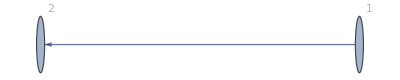

```mathematica
gfdl /@ lattices[2]
```

```mathematica
ltmt /@ lattices[3]
```

{{(1 | 1 | 1
1 | 2 | 2
1 | 2 | 3),(1 | 2 | 3
2 | 2 | 3
3 | 3 | 3)}}

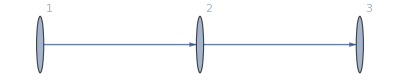

```mathematica
gfdl /@ lattices[3]
```

```mathematica
ltmt /@ lattices[4]
```

{{(1 | 1 | 1 | 1
1 | 2 | 1 | 2
1 | 1 | 3 | 3
1 | 2 | 3 | 4),(1 | 2 | 3 | 4
2 | 2 | 4 | 4
3 | 4 | 3 | 4
4 | 4 | 4 | 4)},{(1 | 1 | 1 | 1
1 | 2 | 2 | 2
1 | 2 | 3 | 3
1 | 2 | 3 | 4),(1 | 2 | 3 | 4
2 | 2 | 3 | 4
3 | 3 | 3 | 4
4 | 4 | 4 | 4)}}

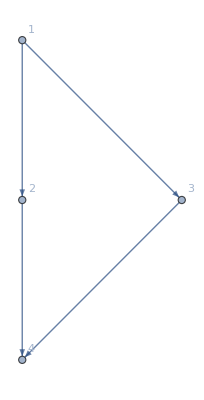
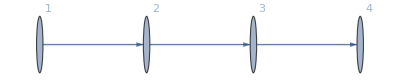

```mathematica
gfdl /@ lattices[4]
```

```mathematica
ltmt /@ lattices[5]
```

{{(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 2
1 | 1 | 3 | 1 | 3
1 | 1 | 1 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 5 | 5 | 5
3 | 5 | 3 | 5 | 5
4 | 5 | 5 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 2
1 | 1 | 3 | 3 | 3
1 | 1 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 5 | 5 | 5
3 | 5 | 3 | 4 | 5
4 | 5 | 4 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 2
1 | 1 | 3 | 3 | 3
1 | 2 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 4 | 4 | 5
3 | 4 | 3 | 4 | 5
4 | 4 | 4 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 2 | 3
1 | 2 | 2 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 3 | 4 | 5
3 | 3 | 3 | 5 | 5
4 | 4 | 5 | 4 | 5
5 | 5 | 5 | 5 | 5)},{(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 3 | 3
1 | 2 | 3 | 4 | 4
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 2 | 3 | 4 | 5
3 | 3 | 3 | 4 | 5
4 | 4 | 4 | 4 | 5
5 | 5 | 5 | 5 | 5)}}

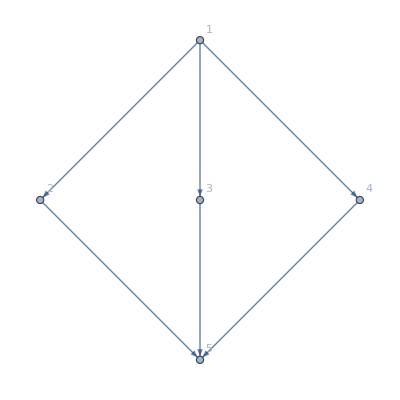
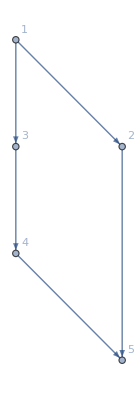
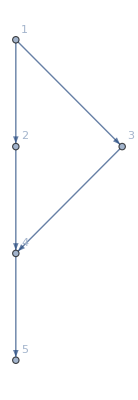
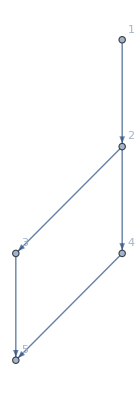
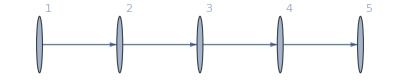

```mathematica
gfdl /@ lattices[5]
```

### Improved

Unable to think of how to do so, so I will give links to algorithms for doing so.

Volker Gebhardt, Stephen Tawn
[1609.08255] Constructing unlabelled lattices
https://arxiv.org/abs/1609.08255

Shoji Kyuno
An Inductive Algorithm to Construct Finite Lattices on JSTOR
https://www.jstor.org/stable/2006054

Peter Jipsen, Nathan Lawless
JipsenLawlessModularLattices20130905.pdf
https://math.chapman.edu/~jipsen/preprints/JipsenLawlessModularLattices20130905.pdf

Jobst Heitzig, Jürgen Reinhold
(PDF) Counting Finite Lattices
https://www.researchgate.net/publication/225384356_Counting_Finite_Lattices

On the Number of Distributive Lattices | The Electronic Journal of Combinatorics
https://www.combinatorics.org/ojs/index.php/eljc/article/view/v9i1r24

Marcel Erné, Jobst Heitzig, Jürgen Reinhold
Nathan Lawless
Generating all modular lattices of a given size
lawless.pdf
https://www.cs.unm.edu/~veroff/ADAM/2013/lawless.pdf